```mathematica
curve=ParametricPlot[{Sin[2t],Cos[3t]},{t,0,2 Pi},PlotStyle->Blue][[1]];
```

```mathematica
circle=Graphics[{Red,Thick,Circle[{0,0},1.5]}][[1]];
```

```mathematica
triangle=Graphics[{Polygon[Table[{1.5 Cos[2 Pi k/3],1.5 Sin[2 Pi k/3]},{k,0,2}]]}][[1]];
```

```mathematica
pentagon=Graphics[{Polygon[Table[{1.5 Cos[2 Pi k/5],1.5 Sin[2 Pi k/5]},{k,0,4}]]}][[1]];
```

```mathematica
line=Graphics[{Black,Thick,Line[{{-1,0},{1,0}}]}][[1]];
```

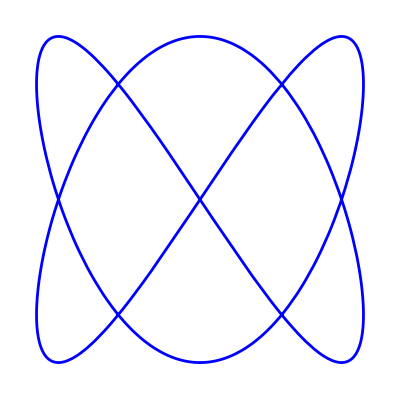
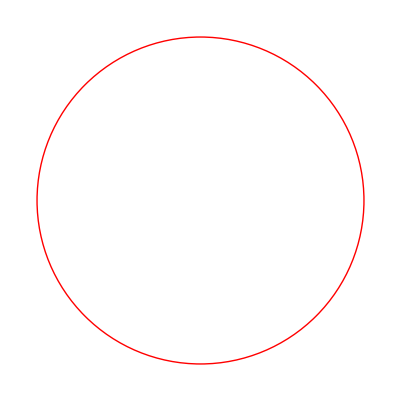
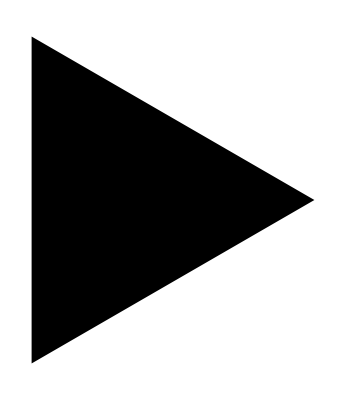
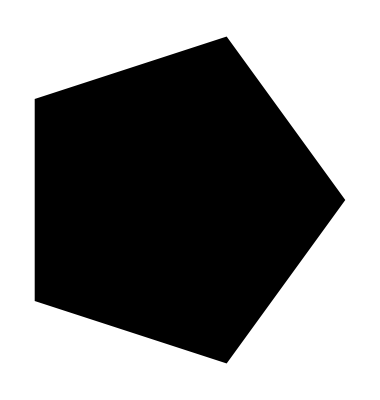
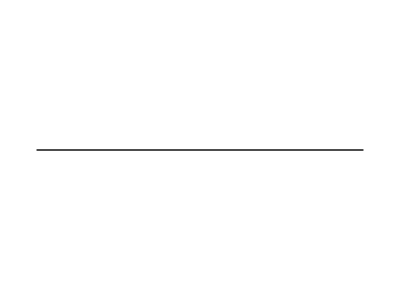

```mathematica
{Graphics[curve],Graphics[circle],Graphics[triangle],Graphics[pentagon],Graphics[line]} (* Show *)
```

```mathematica
transformationF[obj_,a_,center_] :=GeometricTransformation[obj,RotationTransform[a,center]]
```

```mathematica
myMenu=PopupMenu[Dynamic[object],{curve->"Curve",circle->"Circle",triangle->"Triangle",pentagon->"Pentagon",line->"Line"}]
```

```mathematica
Dynamic[mode]
```

```mathematica
mode = {{3,0}->"{3,0}",{0,0}->"origin"}
```

{{3,0}→{3,0},{0,0}→origin}

```mathematica
{Manipulate[Graphics[transformationF[object,a,center],PlotRange->7,Axes->True],{a,0,2*Pi},{center,mode}],myMenu}
```

{,}